```mathematica
M={{0,1,0},
{1,0,0},
{0,0,1}}
```

{{0,1,0},{1,0,0},{0,0,1}}

```mathematica
M.{a,b,cc}
```

{b,a,cc}

```mathematica
alpha={1,0,0,1,1,0,1,1}
```

```mathematica
(* circulant matrix *)

(* left circulant matrix of a given vector alpha*)
Table[RotateLeft[alpha,i],{i,0,Length[alpha]}]//MatrixForm
```

```mathematica
(*left circulant matrix of a given vector alpha *)

Circulant[alpha_]:=Table[RotateRight[alpha,i],{i,0,Length[alpha]}]

M=Circulant[alpha];M//MatrixForm
```

(1 | 0 | 0 | 1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 0 | 1 | 1)

```mathematica
MatrixRank[M,Modulus->2]
```

8

256

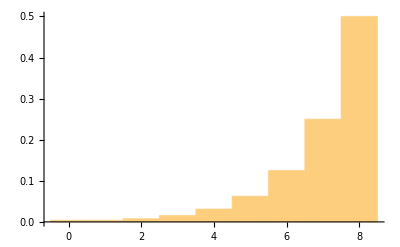

```mathematica
tutte=Map[{M=Circulant[IntegerDigits[#,2,8]],MatrixRank[M,Modulus->2]}&,Range[0,255]];
Length[tutte]
Histogram[Map[Last,tutte],8,"Probability"]
```

```mathematica
R5=Select[tutte,#[[2]]==5&];
```

```mathematica
Map[MatrixForm[First[#]]&,R5]
```

{(0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1),(0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0),(0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1),(0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1),(0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0),(0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1),(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1),(1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0),(1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1),(1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0),(1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1),(1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0 | 0 | 1 | 0),(1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)}